```mathematica
Needs["utilities`"]
ClearAll@poiss;
poiss[λ_?NumericQ,n_]:=Exp[-λ]λ^n/n!;
poiss[λs_List,n_]:=Sum[Exp[-λ] λ^n,{λ,λs}]/n!;
Qprobs[λs_,s_]:=poiss[λs,s]s!
```

```mathematica
Qprobs[{1,2},2]
```

4/ⅇ^2+1/ⅇ

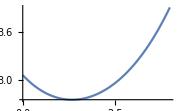

```mathematica
With[{λs=RandomReal[{0,2},8]},
Plot[
Qprobs[λs,m],
{m,0,4},PlotLegends->Automatic,PlotRange->All,ImageSize->Small]
]
```

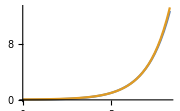
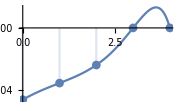

```mathematica
With[{m=4,n=3,λs=RandomReal[{0,2},8]},
Row@{Plot[
{Qprobs[λs,m]^(s-n),Qprobs[λs,n]^(s-m)Qprobs[λs,s]^(m-n)},
{s,0,5},PlotLegends->Automatic,PlotRange->All,ImageSize->Small],
Show[Plot[
Qprobs[λs,m]^(s-n)-Qprobs[λs,n]^(s-m)Qprobs[λs,s]^(m-n),
{s,0,4},PlotLegends->Automatic,PlotRange->All,ImageSize->Small],
DiscretePlot[
Qprobs[λs,m]^(s-n)-Qprobs[λs,n]^(s-m)Qprobs[λs,s]^(m-n),
{s,0,4},Joined->False,PlotMarkers->Automatic]]
}
]
```